```mathematica
f[x_] := x * Cot[x]
```

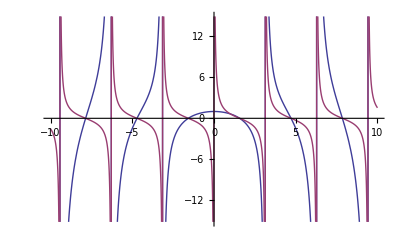

```mathematica
Plot[{f[x], Cot[x]},{x,-10.0,10.0}]
```

```mathematica
For[i = 0,i < 20,i++,Print[N[Pi / 2 + Pi * i]]; Print[FindRoot[f[x] == 2,{x,Pi / 2 + Pi * i}]]; Print["-----"]]
```

```mathematica
g[Pi/  2]
```

2.

```mathematica
g[Pi / 2 + Pi]
```

2.

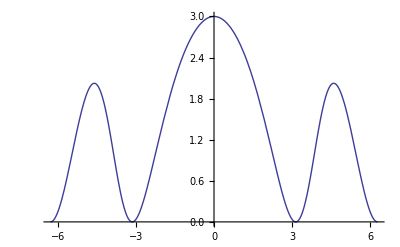

```mathematica
g[k_] := Sin[k]^2 / (0.5 - (Sin[2 * k]) / (4 * k))
Plot[g[k], {k, -2 * Pi, 2 * Pi}]
```

```mathematica
Remove[a]
Sum[1 / (i + 0.5 - a) - 1 / (i + 0.5 + a), {i, n, Infinity}]
```

-PolyGamma[0.,0.5-1. a+n]+1. PolyGamma[0.,0.5+a+n]

```mathematica
bnd[k_, n_] := - 1 / (Pi * k) * (-PolyGamma[0.5 + n + k / Pi] + PolyGamma[0.5 + n - k / Pi])
```

```mathematica
bnd[2.0, 1]
```

0.212453

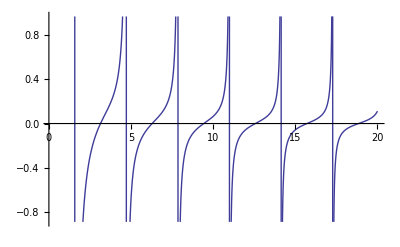

```mathematica
Plot[bnd[k],{k,0.1,20.0}]
```